```mathematica
(*1.3 Задача №3*)
(*1.Функция Гамильтона*)
```

```mathematica
ℋ=p[t]^2/m-a x[t]^2+ b x[t]^4
```

p[t]^2/m-a x[t]^2+b x[t]^4

```mathematica
(*Построим график функции Гамильтона*)
Plot3D[{p^2/m-a x^2+ b x^4}/.{a->1, b->1,m->1},{x,-2,2},{p,-2,2}]
```

-Graphics3D-

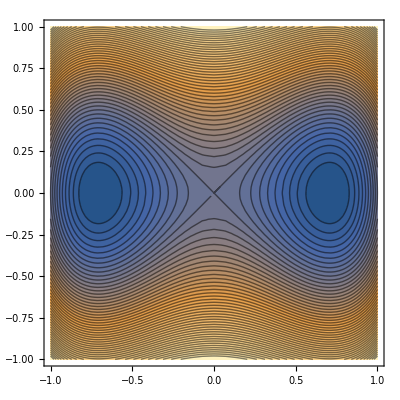

```mathematica
ContourPlot[{p^2/m-a x^2+ b x^4}/.{a->1, b->1,m->1},{x,-1,1},{p,-1,1},Contours->50]
```

```mathematica
(*Анализируя контурный график, можно заметить что в точке (0,0) наибольшее расстояние между соседними энергетическими уровнями а также минимальная крутизна траектории, поэтому в ней частица проводит больше всего времени*)
(*При постоянной энергии частица будет описывать траекторию похожую на цифру 8, причем чем ближе будет частица к центру тем медленнее она будет двигаться*)
```

```mathematica
(*Запишем уравнения Гамильтона*)
```

```mathematica
HamiltonEquations={D[x[t], t]==D[ℋ, p[t]],D[p[t], t]==-D[ℋ, x[t]],x[0]==x0,p[0]==p0}
```

{x'[t]==(2 p[t])/m,p'[t]==2 a x[t]-4 b x[t]^3,x[0]==x0,p[0]==p0}

```mathematica
constants1={a->1,b->1/2,m->1 ,p0->1,x0->0}(*Набор констант в первом случае*)
```

{a→1,b→1/2,m→1,p0→1,x0→0}

```mathematica
NDSolve[HamiltonEquations/.constants1,{x[t],p[t]},{t,0,5}]
```

{{x[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[{t,InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,5}]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
constants2={a->2,b->1/4,m->1 ,p0->0,x0->1}
```

{a→2,b→1/4,m→1,p0→0,x0→1}

```mathematica
NDSolve[HamiltonEquations/.constants2,{x[t],p[t]},{t,0,5}]
```

{{x[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[{t,InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,5}]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(*Найдем функцию Гамильтона вблизи минмиума Энергии*)
```

```mathematica
Solve[D[(-x^2+ x^4), x]==0]
```

{{x→0},{x→-1/(√2)},{x→1/(√2)}}

```mathematica
Normal[Series[x^2+ x,{x,1/(√2),2}]]
```

1/2+1/(√2)+(1+√2) (-1/(√2)+x)+(-1/(√2)+x)^2

```mathematica
ℋ1=p[t]^2/m-1/2+1/(√2)+(1+√2) (-1/(√2)+x[t])+(-1/(√2)+x[t])^2
```

-1/2+1/(√2)+p[t]^2/m+(1+√2) (-1/(√2)+x[t])+(-1/(√2)+x[t])^2

```mathematica
DSolve[{D[x[t], t]==D[ℋ1, p[t]],D[p[t], t]==-D[ℋ1, x[t]],x[0]==x0,p[0]==p0}/.{m->1,x0->0.7,p0->0},{x[t],p[t]},t]
```

{{p[t]→-1.2 Sin[2 t],x[t]→0.5 (2.4 Cos[2 t]-1. Cos[2 t]^2-1. Sin[2 t]^2)}}

```mathematica
ParametricPlot3D[{t,0.5 (2.4 Cos[2 t]-1. Cos[2 t]^2-1. Sin[2 t]^2),-1.2 Sin[2 t]},{t,0,5}]
```

```mathematica
-Graphics3D--Graphics3D-
```